# Unruh-DeWitt detector and unstable mode

(1+1)-dimensional half-Minkowski space

ds^2=-dt^2+dx^2,  x>=0

## Penrose diagram

Half-Minkowski space

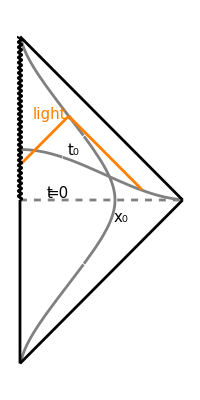

```mathematica
ParametricPlot[{t,1-t},{t,0,1},PlotStyle->Black,Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{t,-1+t},{t,0,1},PlotStyle->Black,Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{0,t},{t,-1,0},PlotStyle->{Black},Axes->False,PlotRange->{-1,1}];
ParametricPlot[{.01Sin[200 t],t},{t,0,1},PlotStyle->{Black},Axes->False,PlotRange->{-1,1}];
ParametricPlot[{1/2-t,1/1.4-t},{t,0.2,2/4.05},PlotStyle->{Orange},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{1/3.3+t,1/1.96-t},{t,0,2/4.48},PlotStyle->{Orange},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[1.2+t]+ArcTan[1.2-t],ArcTan[1.2+t]-ArcTan[1.2-t]},{t,-10,10},PlotStyle->{Gray,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[t+0.5]+ArcTan[t-0.5],ArcTan[t+0.5]-ArcTan[t-0.5]},{t,0,10},PlotStyle->{Gray,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{t,0},{t,0,3},PlotStyle->{Gray,Dashed,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
Graphics[{PointSize[Large],Orange,Point[{1/3.3,1/1.96}],PlotRange->{-1.4,1.4}}];
Show[%,%%,%%%,%%%%,%%%%%,%%%%%%,%%%%%%%,%%%%%%%%,%%%%%%%%%,%%%%%%%%%%,Epilog->{Inset[Style[Subscript[t, 0],FontSize->15],Scaled[{0.34,0.645}]],Inset[Style[Subscript[x, 0],FontSize->15],Scaled[{0.62,0.45}]],Inset[Style[,FontSize->15,Orange],Scaled[{0.2,0.75}]],Inset[Style[t,FontSize->15],Scaled[{0.2,0.52}]],Inset[Style["=0",FontSize->15],Scaled[{0.25,0.52}]]}]
```

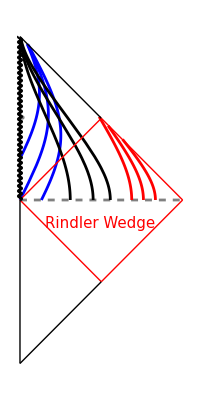

```mathematica
ParametricPlot[{t,1-t},{t,0,.5},PlotStyle->{Black,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{t,1-t},{t,.5,1},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{t,-1+t},{t,0,.5},PlotStyle->{Black,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{t,-1+t},{t,.5,1},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{0,t},{t,-1,0},PlotStyle->{Black,Thick},Axes->False,PlotRange->{-1,1}];
ParametricPlot[{.01Sin[200 t],t},{t,0,1},PlotStyle->{Black},Axes->False,PlotRange->{-1,1}];
ParametricPlot[{1/2-t,1/2-t},{t,0,1/2},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{1/2+t,-1/2-t},{t,-1/2,0},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[.5+t]+ArcTan[.5-t],ArcTan[.5+t]-ArcTan[.5-t]},{t,0,10},PlotStyle->{Black,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[.8+t]+ArcTan[.8-t],ArcTan[.8+t]-ArcTan[.8-t]},{t,0,10},PlotStyle->{Black,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[1.1+t]+ArcTan[1.1-t],ArcTan[1.1+t]-ArcTan[1.1-t]},{t,0,10},PlotStyle->{Black,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->τ/(√(1-v^2)),x->-.2+(v τ)/(√(1-v^2))}/.v->.5,{τ,.37,8},PlotStyle->{Blue,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->τ/(√(1-v^2)),x->0+(v τ)/(√(1-v^2))}/.v->.5,{τ,0,7},PlotStyle->{Blue,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->τ/(√(1-v^2)),x->.2+(v τ)/(√(1-v^2))}/.v->.5,{τ,0,8},PlotStyle->{Blue,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.5,{τ,0,3.8},PlotStyle->{Red,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.4,{τ,0,4.2},PlotStyle->{Red,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.3,{τ,0,5},PlotStyle->{Red,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{t,0},{t,0,3},PlotStyle->{Gray,Dashed,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
Graphics[{PointSize[Small],Gray,Point[{0.01,1/1.96}],PlotRange->{-1.4,1.4}}];
Show[%,%%,%%%,%%%%,%%%%%,%%%%%%,%%%%%%%,%%%%%%%%,%%%%%%%%%,%%%%%%%%%%,%%%%%%%%%%%,%%%%%%%%%%%%,%%%%%%%%%%%%%,%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%,Epilog->{Inset[Style[,FontSize->15,Red],Scaled[{0.5,0.43}]]}]
```

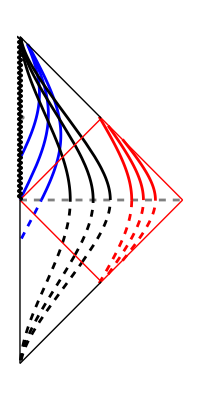

```mathematica
ParametricPlot[{t,1-t},{t,0,.5},PlotStyle->{Black,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{t,1-t},{t,.5,1},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{t,-1+t},{t,0,.5},PlotStyle->{Black,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{t,-1+t},{t,.5,1},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{0,t},{t,-1,0},PlotStyle->{Black,Thick},Axes->False,PlotRange->{-1,1}];
ParametricPlot[{.01Sin[200 t],t},{t,0,1},PlotStyle->{Black},Axes->False,PlotRange->{-1,1}];
ParametricPlot[{1/2-t,1/2-t},{t,0,1/2},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[{1/2+t,-1/2-t},{t,-1/2,0},PlotStyle->{Red,Thick},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[.5+t]+ArcTan[.5-t],ArcTan[.5+t]-ArcTan[.5-t]},{t,0,10},PlotStyle->{Black,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[.5+t]+ArcTan[.5-t],ArcTan[.5+t]-ArcTan[.5-t]},{t,-10,0},PlotStyle->{Black,Thickness[0.005],Dashed},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[.8+t]+ArcTan[.8-t],ArcTan[.8+t]-ArcTan[.8-t]},{t,0,10},PlotStyle->{Black,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[.8+t]+ArcTan[.8-t],ArcTan[.8+t]-ArcTan[.8-t]},{t,-10,0},PlotStyle->{Black,Thickness[0.005],Dashed},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[1.1+t]+ArcTan[1.1-t],ArcTan[1.1+t]-ArcTan[1.1-t]},{t,0,10},PlotStyle->{Black,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[1.1+t]+ArcTan[1.1-t],ArcTan[1.1+t]-ArcTan[1.1-t]},{t,-10,0},PlotStyle->{Black,Thickness[0.005],Dashed},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->τ/(√(1-v^2)),x->-.2+(v τ)/(√(1-v^2))}/.v->.5,{τ,.37,8},PlotStyle->{Blue,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->τ/(√(1-v^2)),x->0+(v τ)/(√(1-v^2))}/.v->.5,{τ,0,7},PlotStyle->{Blue,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->τ/(√(1-v^2)),x->.2+(v τ)/(√(1-v^2))}/.v->.5,{τ,0,8},PlotStyle->{Blue,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->τ/(√(1-v^2)),x->.2+(v τ)/(√(1-v^2))}/.v->.5,{τ,-.32,0},PlotStyle->{Blue,Thickness[0.005],Dashed},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.5,{τ,0,3.8},PlotStyle->{Red,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.5,{τ,-3.8,0},PlotStyle->{Red,Thickness[0.005],Dashed},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.4,{τ,0,4.2},PlotStyle->{Red,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.4,{τ,-4.2,0},PlotStyle->{Red,Thickness[0.005],Dashed},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.3,{τ,0,5},PlotStyle->{Red,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{ArcTan[x+t]+ArcTan[x-t],ArcTan[x+t]-ArcTan[x-t]}/.{t->1/a Sinh[a τ],x->-1/3+1/a Cosh[a τ]}/.a->.3,{τ,-5,0},PlotStyle->{Red,Thickness[0.005],Dashed},Axes->False,PlotRange->{-1.4,1.4}];
ParametricPlot[1/3{t,0},{t,0,3},PlotStyle->{Gray,Dashed,Thickness[0.005]},Axes->False,PlotRange->{-1.4,1.4}];
Graphics[{PointSize[Small],Gray,Point[{0.01,1/1.96}],PlotRange->{-1.4,1.4}}];
Show[%,%%,%%%,%%%%,%%%%%,%%%%%%,%%%%%%%,%%%%%%%%,%%%%%%%%%,%%%%%%%%%%,%%%%%%%%%%%,%%%%%%%%%%%%,%%%%%%%%%%%%%,%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%%%%%%%,%%%%%%%%%%%%%%%%%%%%%%%%%%]
```

## Response function

The probability function is given by

 
 
where I_+= [0,∞) . Using η(τ/T)=Θ(T-τ) in the limit T -> ∞.

### At rest at a fixed position x=x_0

```mathematica
Integrate[Exp[-ⅈ Ω (τ-τl)]Exp[-γ(x0+x0)]Exp[-γ (τ+τl)],{τ,0,∞},{τl,0,∞},Assumptions->{Ω∈Reals,γ>0,x0>0}]
```

ⅇ^(-2 x0 γ)/(γ^2+Ω^2)

Apart from the factor ⅇ^(-2 x0 γ)  we have a non-normalized Breit-Wigner distribution, where γ is the widht indicating the mean life: τ = 1/γ

```mathematica
Integrate[(γ/π)/(γ^2+Ω^2),{Ω,-∞,∞},Assumptions->{γ>0}]
```

1

```mathematica
Series[ⅇ^(-2 x0 γ)/(γ^2+Ω^2),{γ,∞,0}]//Normal
Series[ⅇ^(-2 x0 γ)/(γ^2+Ω^2),{γ,0,0}]//Normal
```

0

1/Ω^2

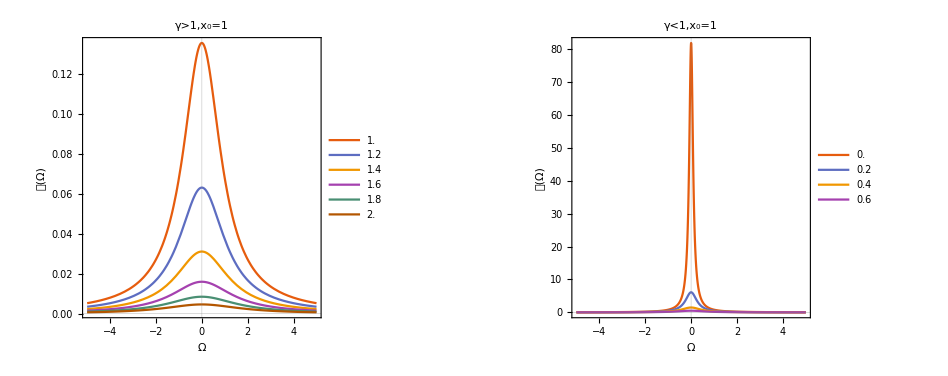

```mathematica
Plot[Evaluate@Table[ⅇ^(-2 x0 γ)/(γ^2+Ω^2)/.x0->1,{γ,1,2,.2}],{Ω,-5,5},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[γ],{γ,1,2,.2}],{{0.84,0.58}}],FrameLabel->{Style[Ω,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ>1,x_0=1"];
Plot[Evaluate@Table[ⅇ^(-2 x0 γ)/(γ^2+Ω^2)/.x0->1,{γ,0.1,.8,.2}],{Ω,-5,5},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[γ],{γ,0,.8,.2}],{{0.84,0.58}}],FrameLabel->{Style[Ω,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ<1,x_0=1"];
GraphicsGrid[{{%%,%}}]
```

### Inertial trajectory

```mathematica
Exp[-γ (x+xl)-γ(t+tl)]/.{t->1/(√(1-v^2))τ,tl->1/(√(1-v^2))τl}/.{x->x0+v/(√(1-v^2))τ,xl->x0+v/(√(1-v^2))τl}//FullSimplify
```

ⅇ^(-2 x0 γ-((1+v) γ (τ+τl))/(√(1-v^2)))

```mathematica
Integrate[Exp[-ⅈ Ω(τ-τl)] ⅇ^(-2 x0 γ-((1+v) γ (τ+τl))/(√(1-v^2))),{τ,0,∞},{τl,0,∞},Assumptions->{γ>0,0<v<1,Ω∈Reals,x0>0}]//FullSimplify
```

(ⅇ^(-2 x0 γ) √(1-v^2))/((√((1+v)/(1-v)) γ+ⅈ Ω) (γ+v γ-ⅈ √(1-v^2) Ω))

```mathematica
Series[(ⅇ^(-2 x0 γ) √(1-v^2))/((√((1+v)/(1-v)) γ+ⅈ Ω) (γ+v γ-ⅈ √(1-v^2) Ω)),{γ,∞,0}]//Normal
Series[(ⅇ^(-2 x0 γ) √(1-v^2))/((√((1+v)/(1-v)) γ+ⅈ Ω) (γ+v γ-ⅈ √(1-v^2) Ω)),{γ,0,0}]//Normal
```

0

1/Ω^2

```mathematica
-((1+v) γ^2)/(-1+v)/.v->1
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Solve[1./(1.2222222222222225+1. Ω^2)==1/(Γ^2/4+Ω^2),Γ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Γ→-2.21108},{Γ→2.21108}}

Plots:

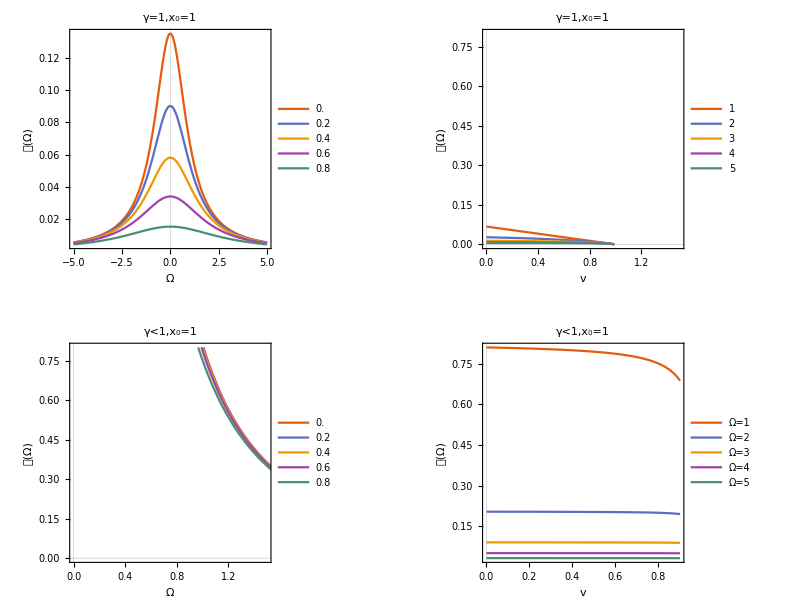

```mathematica
Plot[Evaluate@Table[(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω))/.x0->1/.γ->1,{ν,0,.9,.2}],{Ω,-5,5},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[ν],{ν,0,.9,.2}],{{0.84,0.58}}],FrameLabel->{Style[Ω,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ=1,x_0=1"];
Plot[Evaluate@Table[(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω))/.x0->1/.γ->1,{Ω,1,5,1}],{ν,0,.99},PlotRange->{{0,1.5},{0,.8}},Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[Ω],{Ω,1,5,1}],{{0.84,0.58}}],
FrameLabel->{Style[v,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ=1,x_0=1"];
Plot[Evaluate@Table[(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω))/.x0->1/.γ->.1,{ν,0,.999,.2}],{Ω,-5,5},PlotRange->{{0,1.5},{0,.8}},Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[ν],{ν,0,.9,.2}],{{0.84,0.58}}],FrameLabel->{Style[Ω,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ<1,x_0=1"];
Plot[Evaluate@Table[(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω))/.x0->1/.γ->.1,{Ω,1,5,1}],{ν,0,.9},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["Ω="<>ToString[Ω],{Ω,1,5,1}],{{0.84,0.58}}],
FrameLabel->{Style[v,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ<1,x_0=1"];
GraphicsGrid[{{%%%%,%%%},{%%,%}}]
```

```mathematica
Series[(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω)),{ν,1,0}]
```

O[ν-1]^1

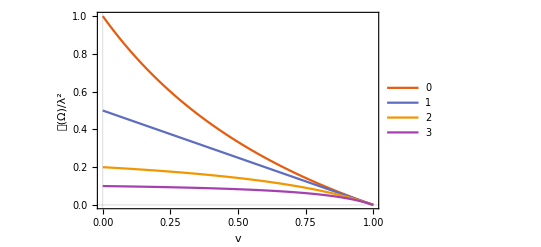

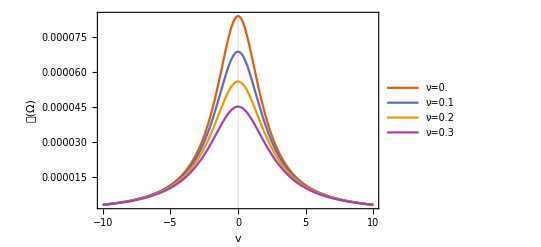

```mathematica
Plot[Evaluate@Table[(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω))/.x0->0/.γ->1,{Ω,0,3,1}],{ν,0,.99999},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[Ω],{Ω,0,3,1}],{{0.84,0.58}}],
FrameLabel->{Style[v,15,Black],Style["𝒫(Ω)/λ^2",17,Black]}]
```

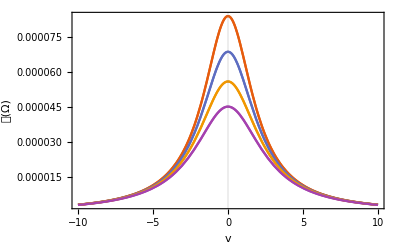

```mathematica
Show[Plot[Evaluate@Table[(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω))/.x0->2/.γ->2,{ν,0,.3,.1}],{Ω,-10,10},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["ν="<>ToString[ν],{ν,0,.9,.1}],{{0.84,0.58}}],
FrameLabel->{Style[v,15,Black],Style["𝒫(Ω)",17,Black]}],Plot[Evaluate@Table[ⅇ^(-2 x0 γ)/(γ^2(1+ν)/(1-ν)+ Ω^2)/.x0->2/.γ->2,{ν,0,.3,.1}],{Ω,-10,10},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["ν="<>ToString[ν],{ν,0,.9,.1}],{{0.84,0.58}}],
FrameLabel->{Style[v,15,Black],Style["𝒫(Ω)",17,Black]}]]
```

```mathematica
Manipulate[Plot[{(ⅇ^(-2 x0 γ) √(1-ν^2))/((γ √((1+ν)/(1-ν))+ⅈ Ω) (γ+γ ν-ⅈ √(1-ν^2) Ω))/.{x0->x1,ν->ν0,γ->1},ⅇ^(-2 x0 γ)/(γ^2(1+ν)/(1-ν)+ Ω^2)/.{x0->x1,ν->ν0,γ->1}},{Ω,-10,10},PlotRange->All,PlotStyle->{Black,Dashed}],{ν0,0,.9},{x1,0,5}]
```

### Accelerated trajectory

```mathematica
Exp[-γ(x+xl)-γ(t+tl)]/.{t->1/a Sinh[a τ],tl->1/a Sinh[a τl]}/.{x->1/a Cosh[a τ],xl->1/a Cosh[a τl]}//FullSimplify
```

ⅇ^(-((ⅇ^(a τ)+ⅇ^(a τl)) γ)/a)

```mathematica
Exp[-ⅈ Ω(τ-0τl)]Exp[-((ⅇ^(a τ)+0 ⅇ^(a τl)) γ)/a]//FullSimplify
```

ⅇ^(-(ⅇ^(a τ) γ)/a-ⅈ τ Ω)

```mathematica
Integrate[Exp[-ⅈ Ω τ-(ⅇ^(a τ) γ)/a],{τ,0,∞},Assumptions->{γ>0,a>0}]Integrate[Exp[ⅈ Ω τ-(ⅇ^(a τ) γ)/a],{τ,0,∞},Assumptions->{γ>0,a>0}]//FullSimplify
```

(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2

```mathematica
Integrate[Exp[-ⅈ Ω(τ-τl)]Exp[-((ⅇ^(a τ)+ⅇ^(a τl)) γ)/a],{τ,0,∞},{τl,0,∞},Assumptions->{a>0,γ>0,Ω∈Reals}]//FullSimplify
```

(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2

```mathematica
(γ/a)^(-ⅈ Ω)Gamma[ⅈ Ω,γ/a](γ/a)^(ⅈ Ω)Gamma[-ⅈ Ω,γ/a]//FullSimplify
```

Gamma[-ⅈ Ω,γ/a] Gamma[ⅈ Ω,γ/a]

```mathematica
Manipulate[Plot[{Gamma[-ⅈ Ω,γ/a] Gamma[ⅈ Ω,γ/a]/.γ->1/.a->a0,(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->1/.a->a0},{Ω,-5,5}],{a0,0.1,10}]
```

```mathematica
Series[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2,{Ω,0,0},Assumptions->{Ω∈Reals,γ>0,a>0}]//Normal//FullSimplify
```

Gamma[0,γ/a]^2/a^2

```mathematica
D[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2,a]//FullSimplify
```

1/a^4(a ⅇ^(-γ/a) (ExpIntegralE[1-(ⅈ Ω)/a,γ/a]+ExpIntegralE[1+(ⅈ Ω)/a,γ/a])+ⅈ Ω Gamma[(ⅈ Ω)/a,γ/a] MeijerG[{{},{1,1}},{{0,0,-(ⅈ Ω)/a},{}},γ/a]-Gamma[-(ⅈ Ω)/a,γ/a] (2 a Gamma[(ⅈ Ω)/a,γ/a]+ⅈ Ω MeijerG[{{},{1,1}},{{0,0,(ⅈ Ω)/a},{}},γ/a]))

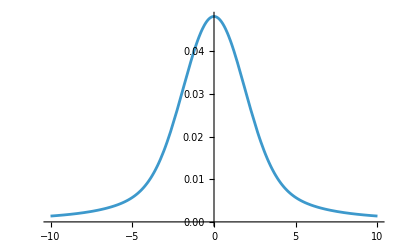

```mathematica
Plot[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.{γ->1,a->1},{Ω,-10,10}]
```

Plots:

General::munfl: Exp[-714.763-2320.81 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.763+2320.81 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.763-2320.81 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

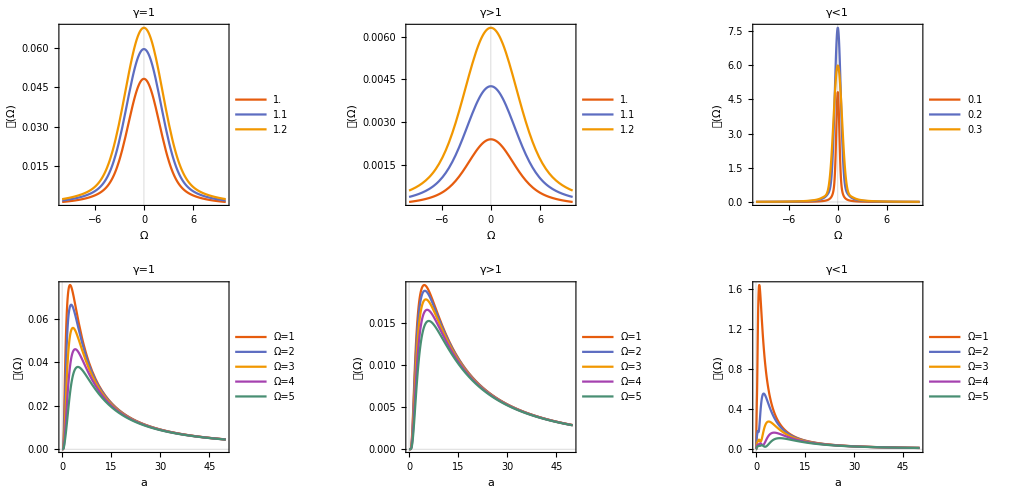

```mathematica
GraphicsGrid[{
{
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->1,{a,1,1.5,.2}],{Ω,-10,10},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,1,1.5,.1}],{{0.84,0.58}}],FrameLabel->{Style[Ω,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ=1"],
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->2,{a,1,1.5,.2}],{Ω,-10,10},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,1,1.5,.1}],{{0.84,0.58}}],FrameLabel->{Style[Ω,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ>1"],
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->.1,{a,.1,.5,.2}],{Ω,-10,10},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,.1,.5,.1}],{{0.84,0.58}}],FrameLabel->{Style[Ω,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ<1"],
},
{
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->1,{Ω,1,5,1}],{a,.01,50},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["Ω="<>ToString[a],{a,1,5,1}],{{0.84,0.58}}],FrameLabel->{Style[,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ=1"],
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->2,{Ω,1,5,1}],{a,.01,50},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["Ω="<>ToString[a],{a,1,5,1}],{{0.84,0.58}}],FrameLabel->{Style[,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ>1"],
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->.1,{Ω,1,5,1}],{a,.01,50},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["Ω="<>ToString[a],{a,1,5,1}],{{0.84,0.58}}],FrameLabel->{Style[,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"γ<1"]
}
}]
```

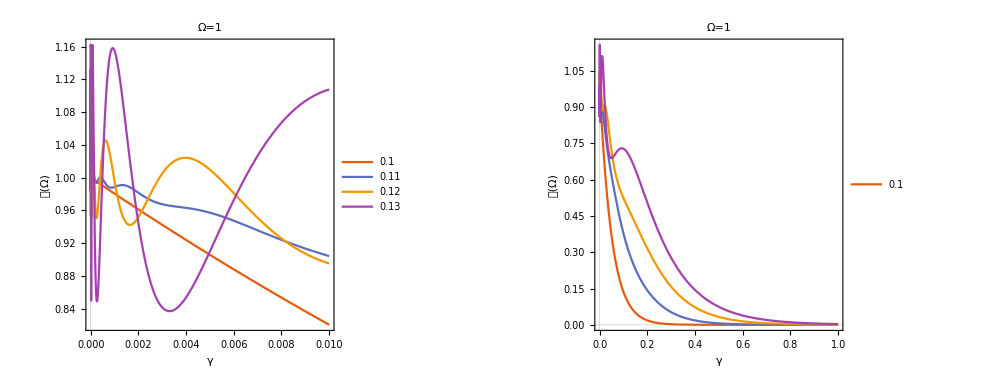

```mathematica
GraphicsGrid[{
{
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.Ω->1,{a,0.1,.4,.1}],{γ,0,.01},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,.1,.4,.01}],{{0.84,0.58}}],FrameLabel->{Style[,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"Ω=1"],
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.Ω->1,{a,0.1,.4,.1}],{γ,0,1},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,.1,.4,1}],{{0.84,0.58}}],FrameLabel->{Style[,13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"Ω=1"]
}
}]
```

```mathematica
Solve[a^2/(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])==Ω^2+Γ^2,Γ]//FullSimplify
```

{{Γ→-(√(a^2-Ω^2 Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a]))/(√Gamma[-(ⅈ Ω)/a,γ/a] √Gamma[(ⅈ Ω)/a,γ/a])},{Γ→(√(a^2-Ω^2 Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a]))/(√Gamma[-(ⅈ Ω)/a,γ/a] √Gamma[(ⅈ Ω)/a,γ/a])}}

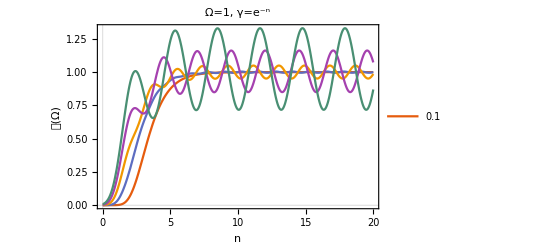

```mathematica
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.Ω->1/.γ->Exp[-n],{a,0.1,.5,.1}],{n,0,20},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,.1,.4,1}],{{0.84,0.58}}],FrameLabel->{Style["n",13,Black],Style["𝒫(Ω)",15,Black]},PlotLabel->"Ω=1, γ=e^-n"]
```

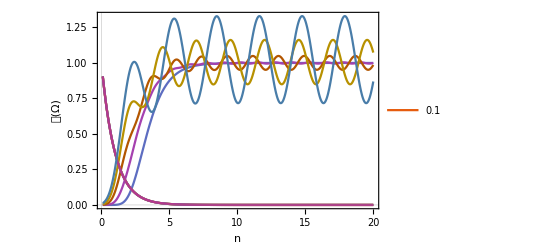

```mathematica
Plot[Evaluate@Table[{Exp[-n],(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.Ω->1/.γ->Exp[-n]},{a,0.1,.5,.1}],{n,0.1,20},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,.1,.4,1}],{{0.84,0.58}}],FrameLabel->{Style["n",13,Black],Style["𝒫(Ω)",15,Black]}]
```

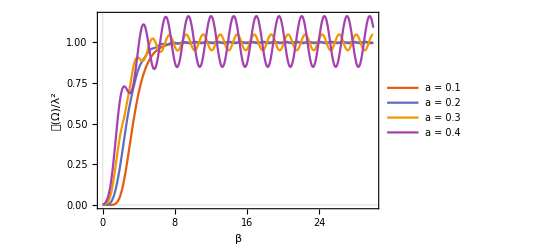

```mathematica
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.Ω->1/.γ->Exp[-β],{a,.1,.4,.1}],{β,0,30},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["a = "<>ToString[a],{a,0.1,0.4,0.1}],{{0.8,0.40}}],FrameLabel->{Style["β",15,Black],Style["𝒫(Ω)/λ^2",17,Black]}]
```

```mathematica
Series[Gamma[-α,γ] Gamma[α,γ],{γ,0,0},Assumptions->{Ω∈Reals,γ>0,a>0}]//Normal//FullSimplify
```

-(γ^-α (1+α γ^α Gamma[-α]) (γ^α-α Gamma[α]))/α^2

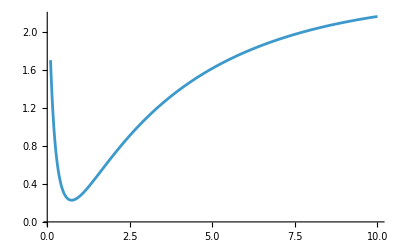

```mathematica
Plot[-(γ^-α (1+α γ^α Gamma[-α]) (γ^α-α Gamma[α]))/α^2/.{α->ⅈ },{γ,0.1,10}]
```

```mathematica
Gamma[-α] Gamma[α]//FullSimplify
```

Gamma[-α] Gamma[α]

```mathematica
Series[Gamma[α,x]Gamma[β,x],{x,0,0}]//Normal
```

(-x^α/α+Gamma[α]) (-x^β/β+Gamma[β])

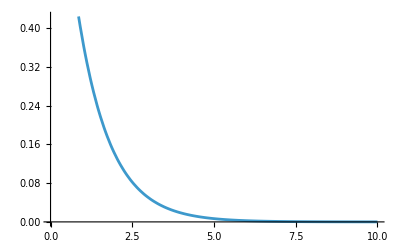

```mathematica
Plot[Exp[-x],{x,0,10}]
```

```mathematica
Log[γ]/.γ->∞
```

∞

```mathematica
1-Exp[0]
```

0

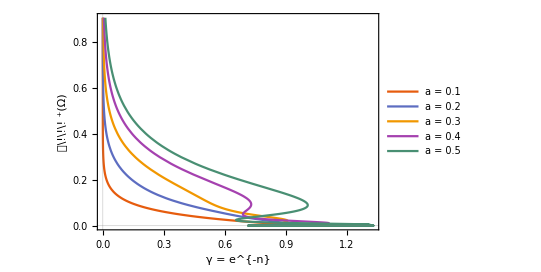

```mathematica
ParametricPlot[Evaluate@Table[{(Gamma[-((I Ω)/a),Exp[-n]/a]*Gamma[(I Ω)/a,Exp[-n]/a])/a^2/. Ω->1,Exp[-n]},{a,0.1,0.5,0.1}],{n,0.1,20},(*a curva será desenhada de n=0.1 até 20=>gamma decresce*)PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["a = "<>ToString[a],{a,0.1,0.5,0.1}],{{0.84,0.58}}],FrameLabel->{Style["γ = e^{-n}",13,Black],Style["𝒫\!\!\! \!\(\*SuperscriptBox[\(\), \(+\)]\)(Ω)",15,Black]},FrameTicks->{Automatic,Automatic}]
```

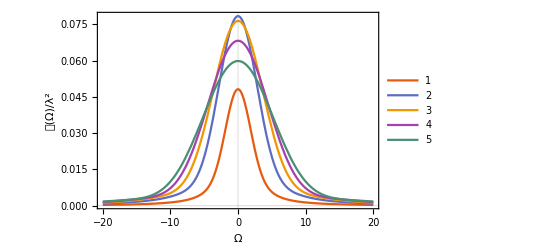

```mathematica
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->1,{a,1,5,1}],{Ω,-20,20},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table[""<>ToString[a],{a,1,5,1}],{{0.88,0.68}}],FrameLabel->{Style[Ω,15,Black],Style["𝒫(Ω)/λ^2",17,Black]}]
```

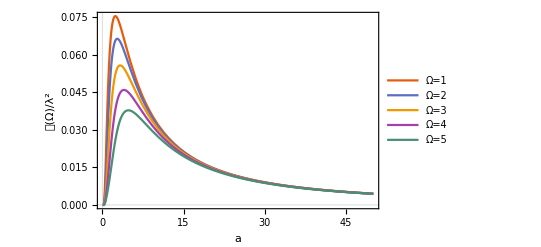

```mathematica
Plot[Evaluate@Table[(Gamma[-(ⅈ Ω)/a,γ/a] Gamma[(ⅈ Ω)/a,γ/a])/a^2/.γ->1,{Ω,1,5,1}],{a,.1,50},PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Placed[Table["Ω="<>ToString[Ω],{Ω,1,5,1}],{{0.84,0.58}}],FrameLabel->{Style[,15,Black],Style["𝒫(Ω)/λ^2",17,Black]}]
```